```mathematica
ClearAll[h,ht]
hzr[s_]:={s,s+1,s-1};
hpr[s_]:={1/s,1/(s+1),1/(s-1)};
hzc[s_]:={(s-(-1+ⅈ))(s-(-1-ⅈ)),(s-(-0.1+ⅈ))(s-(-0.1-ⅈ)),
(s+ⅈ)(s-ⅈ),
(s-(0.1+ⅈ))(s-(0.1-ⅈ)),(s-(1+ⅈ))(s-(1-ⅈ))};
hpc[s_]:={1/((s-(-1+ⅈ))(s-(-1-ⅈ))),1/((s-(-0.1+ⅈ))(s-(-0.1-ⅈ))),
1/((s+ⅈ)(s-ⅈ)),
1/((s-(0.1+ⅈ))(s-(0.1-ⅈ))),1/((s-(1+ⅈ))(s-(1-ⅈ)))};
```

```mathematica
Table[{
(*h[s][[k]],*)
LogLogPlot[{Abs[hzr[ⅈ x][[k]]]},{x,0.01,100},PlotRange->{0.01,100},PlotTheme->"Monochrome",AxesLabel->{"ω","|H(s)|"}],
LogLinearPlot[{180/π*Arg[hzr[ⅈ x][[k]]]},{x,0.01,100},PlotRange->{0,190},PlotTheme->"Monochrome",AxesLabel->{"ω","∠H(s)"},Exclusions->None,Ticks->{Automatic,{0,45,90,135,180}}],
(*InverseLaplaceTransform[h[s][[k]],s,t],*)
Plot[Convolve[InverseLaplaceTransform[hzr[s][[k]],s,t],Sin[t],t,x],{x,0,4 π},PlotRange->{-2,2},PlotTheme->"Monochrome",AxesLabel->{"t/s","h(t)"},Ticks->{None,Automatic}]
},{k,1,3}]
```

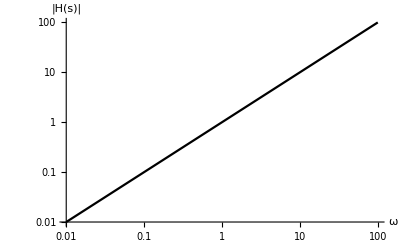
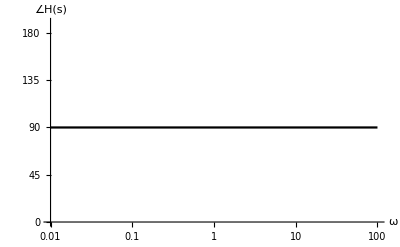
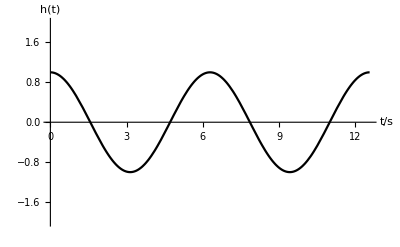
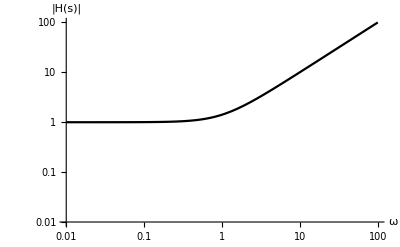
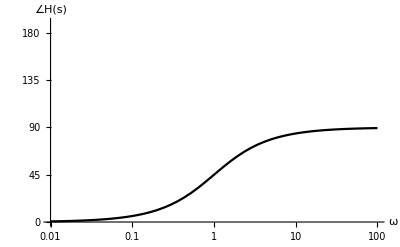
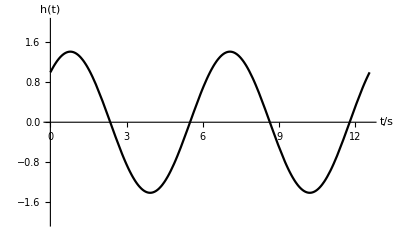
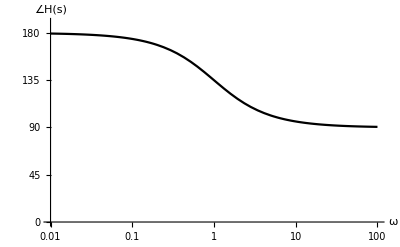
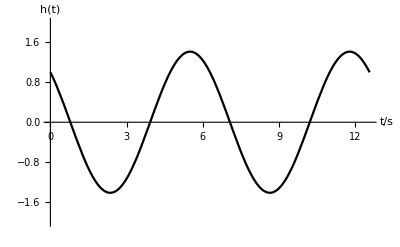
```mathematica
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}
```

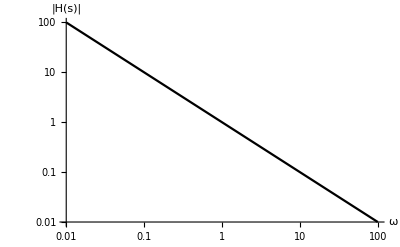
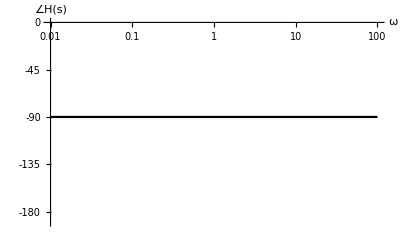
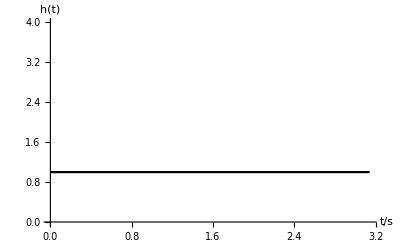
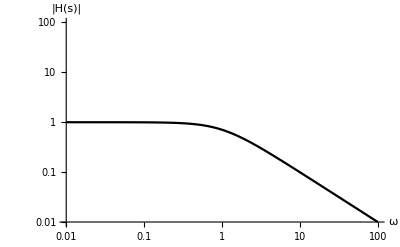
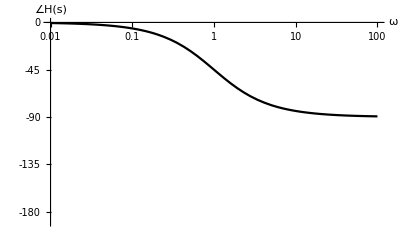
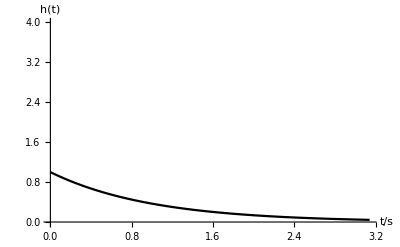
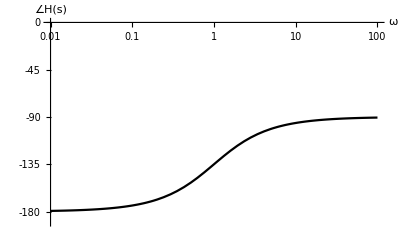
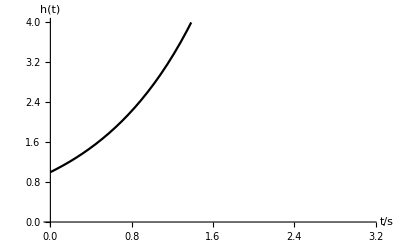
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[{
(*h[s][[k]],*)
LogLogPlot[{Abs[hpr[ⅈ x][[k]]]},{x,0.01,100},PlotRange->{0.01,100},PlotTheme->"Monochrome",AxesLabel->{"ω","|H(s)|"}],
LogLinearPlot[{180/π*Arg[hpr[ⅈ x][[k]]]},{x,0.01,100},PlotRange->{-190,0},PlotTheme->"Monochrome",AxesLabel->{"ω","∠H(s)"},Exclusions->None,Ticks->{Automatic,{0,-45,-90,-135,-180}}],
(*InverseLaplaceTransform[h[s][[k]],s,t],*)
Plot[InverseLaplaceTransform[hpr[s][[k]],s,t],{t,0, π},PlotRange->{0,4},PlotTheme->"Monochrome",AxesLabel->{"t/s","h(t)"},Ticks->{None,Automatic}]
},{k,1,3}]
```

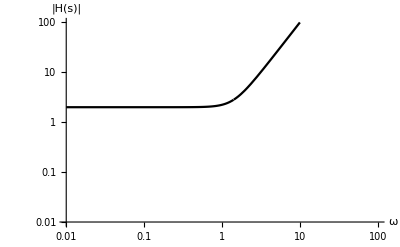
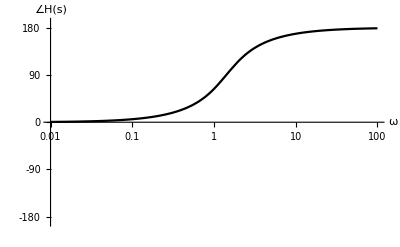
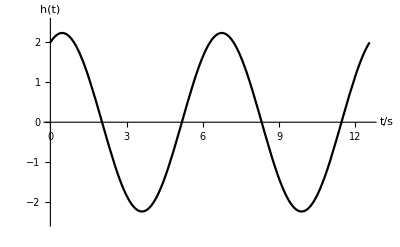
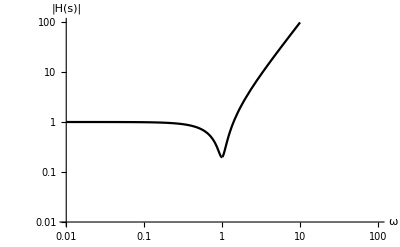
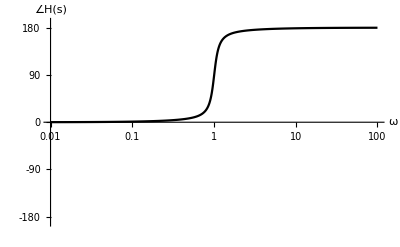
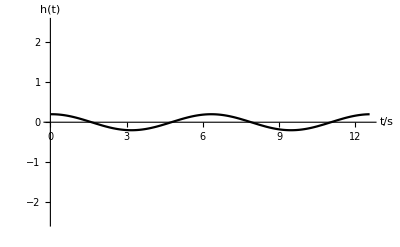
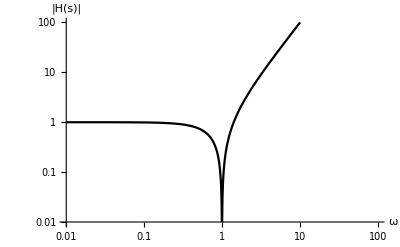
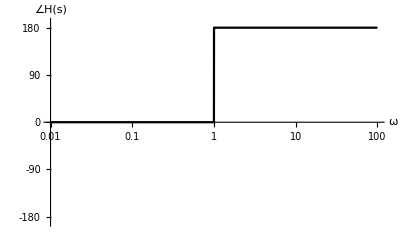
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[{
(*h[s][[k]],*)
LogLogPlot[{Abs[hzc[ⅈ x][[k]]]},{x,0.01,100},PlotRange->{0.01,100},PlotTheme->"Monochrome",AxesLabel->{"ω","|H(s)|"}],
LogLinearPlot[{180/π*Arg[hzc[ⅈ x][[k]]]},{x,0.01,100},PlotRange->{-190,190},PlotTheme->"Monochrome",AxesLabel->{"ω","∠H(s)"},Exclusions->None,Ticks->{Automatic,{180,90,0,-90,-180}}],
(*InverseLaplaceTransform[h[s][[k]],s,t],*)
Plot[Convolve[InverseLaplaceTransform[hzc[s][[k]],s,t],Sin[t],t,x],{x,0,4 π},PlotRange->{-2.5,2.5},PlotTheme->"Monochrome",AxesLabel->{"t/s","h(t)"},Ticks->{None,Automatic}]
},{k,1,5}]
```

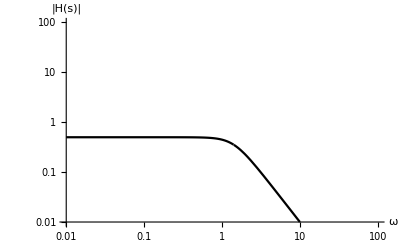
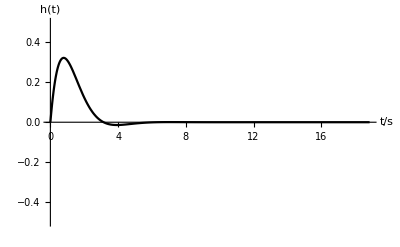
{{-Graphics-,-Graphics-,-Graphics-}}

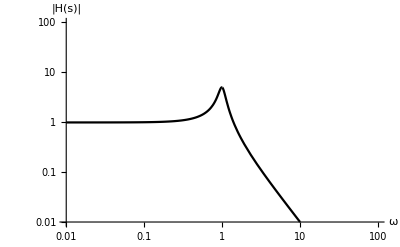
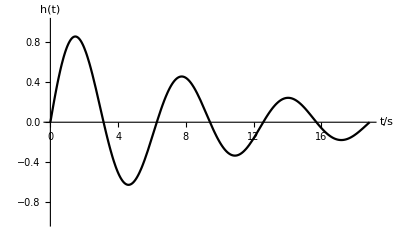
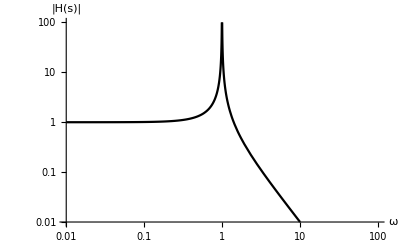
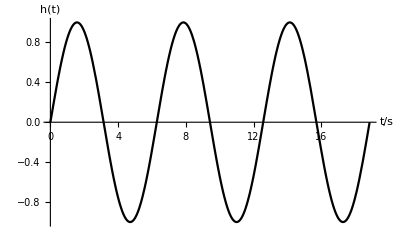
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

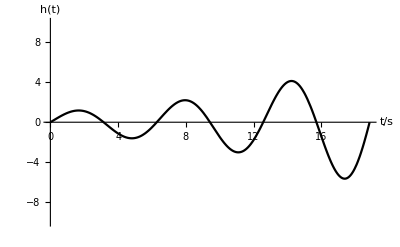
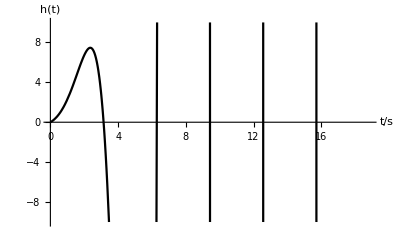
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[{
(*h[s][[k]],*)
LogLogPlot[{Abs[hpc[ⅈ x][[k]]]},{x,0.01,100},PlotRange->{0.01,100},PlotTheme->"Monochrome",AxesLabel->{"ω","|H(s)|"}],
LogLinearPlot[{180/π*Arg[hpc[ⅈ x][[k]]]},{x,0.01,100},PlotRange->{-190,190},PlotTheme->"Monochrome",AxesLabel->{"ω","∠H(s)"},Exclusions->None,Ticks->{Automatic,{180,90,0,-90,-180}}],
(*InverseLaplaceTransform[h[s][[k]],s,t],*)
Plot[InverseLaplaceTransform[hpc[s][[k]],s,t],{t,0, 6π},PlotRange->{-0.5,0.5},PlotTheme->"Monochrome",AxesLabel->{"t/s","h(t)"},Ticks->{None,Automatic}]
},{k,1,1}]
Table[{
(*h[s][[k]],*)
LogLogPlot[{Abs[hpc[ⅈ x][[k]]]},{x,0.01,100},PlotRange->{0.01,100},PlotTheme->"Monochrome",AxesLabel->{"ω","|H(s)|"}],
LogLinearPlot[{180/π*Arg[hpc[ⅈ x][[k]]]},{x,0.01,100},PlotRange->{-190,190},PlotTheme->"Monochrome",AxesLabel->{"ω","∠H(s)"},Exclusions->None,Ticks->{Automatic,{180,90,0,-90,-180}}],
(*InverseLaplaceTransform[h[s][[k]],s,t],*)
Plot[InverseLaplaceTransform[hpc[s][[k]],s,t],{t,0, 6π},PlotRange->{-1,1},PlotTheme->"Monochrome",AxesLabel->{"t/s","h(t)"},Ticks->{None,Automatic}]
},{k,2,3}]
Table[{
(*h[s][[k]],*)
LogLogPlot[{Abs[hpc[ⅈ x][[k]]]},{x,0.01,100},PlotRange->{0.01,100},PlotTheme->"Monochrome",AxesLabel->{"ω","|H(s)|"}],
LogLinearPlot[{180/π*Arg[hpc[ⅈ x][[k]]]},{x,0.01,100},PlotRange->{-190,190},PlotTheme->"Monochrome",AxesLabel->{"ω","∠H(s)"},Exclusions->None,Ticks->{Automatic,{180,90,0,-90,-180}}],
(*InverseLaplaceTransform[h[s][[k]],s,t],*)
Plot[InverseLaplaceTransform[hpc[s][[k]],s,t],{t,0, 6π},PlotRange->{-10,10},PlotTheme->"Monochrome",AxesLabel->{"t/s","h(t)"},Ticks->{None,Automatic}]
},{k,4,5}]
```

```mathematica
Solve[{a^2+b^2==ω^2,a==ζ ω,2ζ==1/Q},{ω,ζ,Q}]
```

{{ω→-√(a^2+b^2),ζ→-a/(√(a^2+b^2)),Q→-(√(a^2+b^2))/(2 a)},{ω→√(a^2+b^2),ζ→a/(√(a^2+b^2)),Q→(√(a^2+b^2))/(2 a)}}

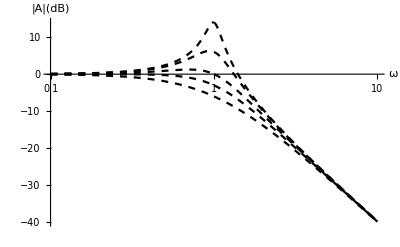

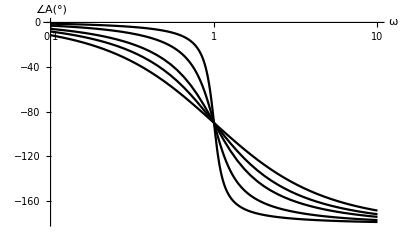

```mathematica
ωp=1;
h[s_,Q_]:=1/(s^2+ωp/Q s+ωp^2);
LogLinearPlot[20*Log10[Abs[h[ⅈ*ω,{0.5,0.707,1,2,5}]]],{ω,0.1,10},PlotTheme->"Monochrome",AxesLabel->{"ω","|A|(dB)"},PlotStyle->{Dashed}]
LogLinearPlot[180/π*Arg[h[ⅈ*ω,{0.5,0.707,1,2,5}]],{ω,0.1,10},PlotTheme->"Monochrome",AxesLabel->{"ω","∠A(°)"}]
```